LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{Log[17],-4.60517},{Log[26],-4.19971},{3.54096,-3.81671},{3.74479,-3.91202},{Log[50],-3.8397},{4.10594,-3.61192},{Log[65],-3.64966},{4.28359,-3.64966},{Log[80],-3.64966},{4.46361,-3.50656},{4.56226,-3.38139},{4.61016,-3.32424},{4.6747,-3.21888},{Log[114],-3.10109},{4.8941,-2.83022},{4.98498,-2.67365},{Log[165],-2.48891},{5.2428,-2.35388},{Log[195],-2.20727},{Log[207],-2.16282},{Log[236],-1.87732},{5.55567,-1.68201},{5.63049,-1.54178},{Log[303],-1.34707},{5.7994,-1.15518},{5.96229,-0.798508},{Log[425],-0.616186},{6.11102,-0.478036},{6.16584,-0.356675},{Log[500],-0.248461},Null},x,x]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit :: notdata will be suppressed during this calculation.

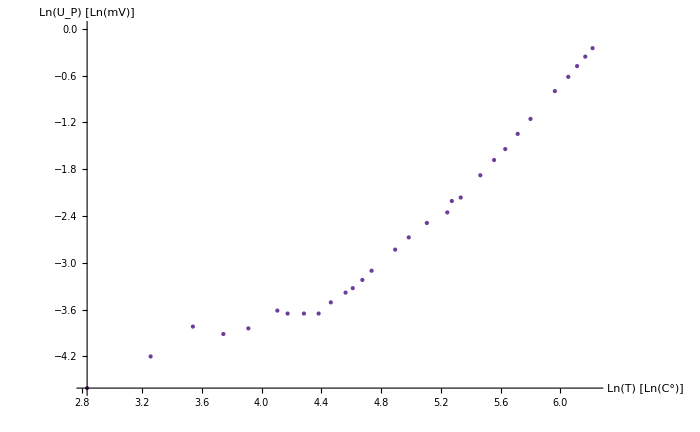

```mathematica
(* Aufgabe 2.1 *)
punkte={{Log[17],Log[0.01]},{Log[26],Log[0.015]},{Log[34.5],Log[0.022]},{Log[42.3],Log[0.02]},{Log[50],Log[0.0215]},{Log[60.7],Log[0.027]},{Log[65],Log[0.026]},{Log[72.5],Log[0.026]},{Log[80],Log[0.026]},{Log[86.8],Log[0.03]},{Log[95.8],Log[0.034]},{Log[100.5],Log[0.036]},{Log[107.2],Log[0.04]},{Log[114],Log[0.045]},{Log[133.5],Log[0.059]},{Log[146.2],Log[0.069]},{Log[165],Log[0.083]},{Log[189.2],Log[0.095]},{Log[195],Log[0.11]},{Log[207],Log[0.115]},{Log[236],Log[0.153]},{Log[258.7],Log[0.186]},{Log[278.8],Log[0.214]},{Log[303],Log[0.26]},{Log[330.1],Log[0.315]},{Log[388.5],Log[0.45]},{Log[425],Log[0.54]},{Log[450.8],Log[0.62]},{Log[476.2],Log[0.7]},{Log[500],Log[0.78]},};

model=LinearModelFit[punkte,x,x]
Show[ListPlot[punkte],Plot[model["BestFit"],{x,-4,4}],AxesLabel->{"Ln(T) [Ln(C°)]", "Ln(U_P) [Ln(mV)]"}]
```